# Bulge To Spike

If I have a Hessenberg matrix with a bulge in it. I can transform the bulge to two spikes using a small orthogonal matrix Q

### SchurDecomposition

The Schur decomposition of a matrix is essentially a eigenvalue decomposition except it forces orthogonal transformations. As a result it can not go to diagonal. It goes to essentially upper triangular.

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}];
{Q,T}=SchurDecomposition[A];
TabView[{
"A"->MatrixPlot[A],
"T"->MatrixPlot[T],
"Qᵀ.A.Q"->MatrixPlot[Qᵀ.A.Q]
},2]
```

123

### Bulge to Spike

I can use the Schur decomposition of the bulge to reduce a bulge on a Hessenberg matrix to a couple of spikes.

```mathematica
{m,s,b}={56,24,14};
SetOptions[MatrixPlot,ColorRules->{0->LightGreen}];
A=RandomReal[{-1,1},{m,m}];
H=HessenbergDecomposition[A]⟦2⟧;
H⟦s+1;;s+b,s+1;;s+b⟧=RandomReal[{-1,1},{b,b}];
B=H⟦s+2;;s+b-1,s+2;;s+b-1⟧;
{Q,T}=SchurDecomposition[B];
BigQ=IdentityMatrix[m]; 
BigQ⟦s+2;;s+b-1,s+2;;s+b-1⟧=Q;
Spike=Chop[BigQᵀ.H.BigQ];
TabView[{
"H"->MatrixPlot[Chop[H],Mesh->{{s,s+b},{s,s+b}}],
"QᵀBQ"->MatrixPlot[Chop[Qᵀ.B.Q]],
"BigQᵀHBigQ"->MatrixPlot[Spike,Mesh->{{s,s+b},{s,s+b}}]
}]
```

123

If the far corners of the spike are zero the eigenvalue problem decouples.

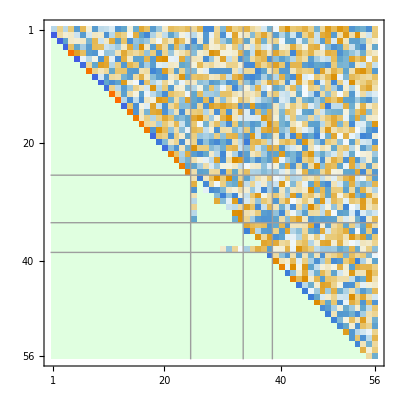

```mathematica
r=6;
NewSpike=UpperTriangularize[Spike,r-b];
MatrixPlot[NewSpike,Mesh->{{s+1,s+b-r+1,s+b},{s,s+b-r+1,s+b}}]
```